Buffon[NumberOfNeedles, NeedleSize, SurfaceDimension, GridWidth, Show → True/ Parallelize]
e.g: Buffon[35,2,20,3,Show→True]

Options:
Show→...
True: Everything 
Parallelize: Pi Estimation using Parallelization (fastest)


Kernels: Optional for even better parallelization
Launch amount of Logical CPU Cores (usually twice the physical cores/check in task manager)

```mathematica
launch[LogicalCores_]:=Quiet@Which[LogicalCores>8,Print["Input Maximum of 8"],$KernelCount==8,Print["Done"],$KernelCount!=0,LaunchKernels[LogicalCores-$KernelCount];Print["Done"],N[$KernelCount==0],LaunchKernels[LogicalCores];Print["Done"]]
```

```mathematica
launch[8]
```

Done

```mathematica
(********************************************************************************************************************)
```

```mathematica
ClearAll@Buffon;
Options[Buffon]={Show->True};
Buffon::usage="Buffon[NumberOfNeedles,NeedleSize,SurfaceDimension,GridWidth,Options_Show_True_Parallelize]";
FE`CacheTemplateAndUsage["Buffon"];
Buffon[iterate_,linesize_,plotrange_,width_,OptionsPattern[]]:=

(***********************************************************************************************************)
(*LOCAL VARIABLES*)

Quiet@Module[
{a,b,h,bound,randomised,rules,equation,Plotting,FirstCoList,contour,endpoint,SecondCo,intersections,x,y,
GridPlot,SecondPlot,SecondPlotCircle,SecondEndPlot,FirstPlot,NeedlePlot,calculate,
ColourList=RandomColor[iterate]}(*List of Random Colours*),

Catch[Check[
(***********************************************************************************************************)
(*PI ESTIMATE FOR PI ESTIMATION ONLY*)
calculate:=ParallelTable[

ClearAll[a,b,h,equation,randomised](*Clear variables every new iteration*);

a=RandomReal[{0,N[plotrange]}](*random x coordinate*);
b=RandomReal[{0,N[plotrange]}](*random y coordinate*);

h=Part[First[Part[Quiet[NSolve[
linesize^2==(x-a)^2+(y-b)^2,RandomChoice[{x,y}],
Reals]],RandomInteger[{1,2}]]],2];

randomised=RandomReal[Flatten[
RegionBounds@(*Transform region to bounds*)
ImplicitRegion[#,x]&/@(*Transform inequality to region *)
({Quiet@Reduce[ReplaceAll[Part[h,2],y->x],x,Reals]})(*Extract Domain of Semicircle Equation*)
]];

(*Intersections*)
MemberQ[(*Give True if "True" is present in list*)
IntervalMemberQ[(*generate list for True where gridline⊂domain of line and false otherwise *)

(*Domain of line*)
Interval[ 
If[Variables[h[[1]]]==={y},(*if semicircle is in terms of y*)
Sort[{a,ReplaceAll[h[[1]],y->randomised]}],
Sort[{a,randomised}]]],

(*Interval of Gridlines*)
Interval/@Table[{a,a},{a,0,plotrange+width,width}]],
True],

iterate];
(***********************************************************************************************************)
(*PARALLELIZE*)

If[OptionValue[Show]===Parallelize,Throw@
N[linesize*((2 *iterate)/(Count[Quiet[calculate],True]*width))]];
(***********************************************************************************************************)
(*DATA*)

If[OptionValue[Show]===Data,
Throw@N[calculate]];
(***********************************************************************************************************)
(*CALCULATIONS FOR PLOTTING*)
If[OptionValue[Show]===True,
rules=Dispatch[Part[(*Extract rules of Reap*)
Reap[
Quiet@Do[(*Reiterate for different random values a,b*)

ClearAll[a,b,h,equation,randomised,bound](*Clear variables every new iteration*);

a=RandomReal[{0,N[plotrange]}](*random x coordinate*);
b=RandomReal[{0,N[plotrange]}](*random y coordinate*);

(*Random Coordinates*)
Sow[{a,b},FirstCoList](*Append coordinate to FirstCoList*);

(*Semicircle conditional expression*)
equation=NSolve[
Sow[linesize^2==(x-a)^2+(y-b)^2,Plotting],RandomChoice[{x,y}],(*solve for either x or y*)
Reals][[RandomInteger[{1,2}]]];(*choose top or bottom/left or right of semicircle*)

(*Semicircle equation "="*)
Sow[
ReplaceAll[First[Normal[equation]],Rule->Equal],(*extract equation and transform -> to = *)
contour];

(*Semicircle conditional expression Values only*)
h=Part[First[equation],2];

(*(*Semicircle Equations "→"*)
Sow[h[[1]],EquationList](*Extract semicircle equation and append to "EquationList"*);*)

(*Domain {Subscript[x, min],Subscript[x, max]}*)
bound=
Flatten[
RegionBounds@(*Transform region to bounds*)
ImplicitRegion[#,x]&/@(*Transform inequality to region *)
({Quiet@Reduce[ReplaceAll[Part[h,2],y->x],x,Reals]})(*Extract Domain of Semicircle Equation*)
];

(*Random x or y coordinate of second point to connect with midpoint*)
randomised=RandomReal[bound];(*Generate random number with a domain of semicircle equation*)

(*{x,y} Coordinate of second point connecting line*)
Sow[
If[Variables[h[[1]]]==={y},(*if equation is in terms of Y*)
{ReplaceAll[h[[1]],y->randomised],randomised},(*substitute random y to find x*)
{randomised,ReplaceAll[h[[1]],x->randomised]}],(*substitute random x to find y*)
SecondCo];

(*Endpoints of semicircle*)
Sow[
If[Variables[h[[1]]]==={y},(*if equation is in terms of Y*)
Table[{a,y},{y,bound}],(* {Subscript[midpoint, x] , Subscript[range, y]}*)
Table[{x,b},{x,bound}](* {Subscript[Domain, x], Subscript[midpoint, y]}*)
],endpoint];

(*Intersections*)
Sow[MemberQ[(*Give True if "True" is present in list*)
IntervalMemberQ[(*generate list for True where gridline∈domain of line and false otherwise *)

(*Domain of line*)
Interval[ 
If[Variables[h[[1]]]==={y},(*if semicircle is in terms of y*)
Sort[{a,ReplaceAll[h[[1]],y->randomised]}],
Sort[{a,randomised}]]],

(*Interval of Gridlines*)
Interval/@Table[{a,a},{a,0,plotrange+width,width}]],
True],
intersections];,

iterate](*Reiterate "iterate" times*)
,_,Rule](*Reap as rules*)
,2]];

(***********************************************************************************************************)
(*DEFINING PLOTS*)


(*Grid Lines*)
GridPlot=ContourPlot[(##1&)[](*Empty Plot*)
,{x,0-linesize,plotrange+linesize},{y,0-linesize,plotrange+linesize},GridLines->{Range[0,plotrange+width,width],None},GridLinesStyle->Directive[Black,Dotted],AspectRatio->Automatic];

(*Define Plot Circle of possible second points*)
SecondPlotCircle=ContourPlot[Evaluate@ReplaceAll[Plotting,rules],{x,-linesize,plotrange+linesize},{y,-linesize,plotrange+linesize},AspectRatio->Automatic,ContourStyle->ColourList];

(*Define Plot Semicircle of possible second points*)
SecondPlot=ContourPlot[Evaluate@ReplaceAll[contour,rules],{x,-linesize,plotrange+linesize},{y,-linesize,plotrange+linesize},AspectRatio->Automatic,ContourStyle->ColourList];

(*Define Plot of predefined Random Coordinates*)
FirstPlot=ListPlot[
Tooltip[{#}&/@ReplaceAll[FirstCoList,rules](*wrap {} around each coordinate to allow for different colours*)
],PlotStyle->ColourList,AspectRatio->Automatic,Axes->False,Frame->True];

(*Define Plot of Semicircle Endpoints*)
SecondEndPlot=ListPlot[Tooltip[{#}&/@(*wrap {} around each coordinate to allow for different colours*)
Flatten[ReplaceAll[endpoint,rules],1]],(*Create {x,y} coordinates by tranposing a list of X and Y coordinates*)
PlotStyle->Map[Sequence@@ConstantArray[#,2]&,ColourList],(*Double every colour in list as semicircles have 2 endpoints*)
Axes->False,Frame->True,AspectRatio->Automatic];

(*Define Plot of Needle*)
NeedlePlot=ListLinePlot[Tooltip@Transpose[{FirstCoList/.rules,SecondCo/.rules}],(*Create {x,y} by transposing a list of x and y coordinates*)
Axes->False,Frame->True,AspectRatio->Automatic,PlotStyle->ColourList];

(***********************************************************************************************************)
(*DISPLAY*)
(***********************************************************************************************************)
(*Text*)

Manipulate[
TableForm[{
Style[Column[{

Row[{"N: Number of Needles ",iterate}],
Row[{"L: Needle Length: ",linesize}],
Row[{"W : Grid width: ",width}],
Row[{"I: Intersections: ",Count[ReplaceAll[intersections,rules],True]}],
Row[{"Estimating Pi: (2  L  N)/(I  W) → ",Row[{2," x ",linesize ," x ",iterate}]/Row[{Count[ReplaceAll[intersections,rules],True]," x ",width}]," → ",Style[N[linesize*((2 *iterate)/(Count[ReplaceAll[intersections,rules],True]*width))],FontSize->13,Bold]}]

}],FontSize->14],
(***********************************************************************************************************)
(*SHOW PLOTS*)

Show[
{(*GridLines*)
If[lines==1,GridPlot,##&[]],

(*Blank*)
ContourPlot[(##1&)[],{x,0-linesize,plotrange+linesize},{y,0-linesize,plotrange+linesize},AspectRatio->Automatic],

(*Circle*)
If[circle==1,SecondPlotCircle,##&[]],

(*Semicircle*)
If[Semicircle==1,SecondPlot,##&[]],

(*Random Coordinates*)
If[RandomCo==1,FirstPlot,##&[]],

(*Semicircle Endpoints*)
If[Endpoint==1,SecondEndPlot,##&[]],

(*Needle Line*)
If[Needle==1,NeedlePlot,##&[]]},

ImageSize->{400,400}
]
}],
(***********************************************************************************************************)
(*CHECKBOXES*)

(*GridLines*)
{{lines,1,Style["GridLines",FontSize->14]},{1,0}},

(*Random Coordinates*)
{{RandomCo,0,Style["Random First Points",FontSize->14]},{1,0}},

(*Circle*)
{{circle,0,Style["Possible Second Points Circle",FontSize->14]},{1,0}},

(*Semicircle*)
{{Semicircle,0,Style["Possible Second Points SemiCircle",FontSize->14]},{1,0}},

(*Endpoint*)
{{Endpoint,0,Style["Semicircle Endpoints",FontSize->14]},{1,0}},

(*Needle*)
{{Needle,0,Style["Needle",FontSize->14]},{1,0}},
ControlPlacement->{Top}(*CheckBox Position*)

]


]
(***********************************************************************************************************)
,Throw[0]]](*give 0 if no intersections*)


]
```

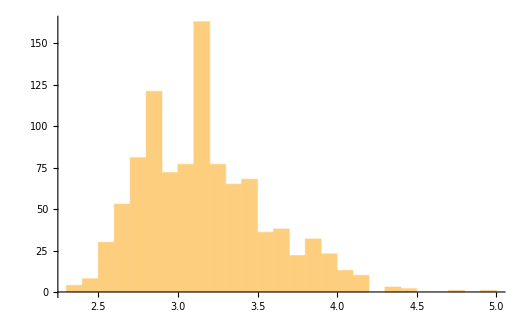

```mathematica
Histogram[ParallelTable[Buffon[100,2,100,3,Show->Parallelize],1000],{0.1},GridLines->{{π},None},Method->{"GridLinesInFront"->True},GridLinesStyle->Directive[Red,Thick]]
```

```mathematica
(***********************************************************************************************************)
```

```mathematica
BuffonData[iterate_,linesize_,plotrange_,width_]:=Module[{a=0},ListLinePlot[Transpose[{Range[iterate],N[MapThread[Quiet@Catch[Check[(2 linesize*#2)/(#1  width),Throw[0]]]&,{Accumulate@Boole@Buffon[iterate,linesize,plotrange,width,Show->Data],Range[iterate]}]]}],GridLines->{None,{π}},GridLinesStyle->Directive[Red,Thick],PlotRange->{2,4}]]
```

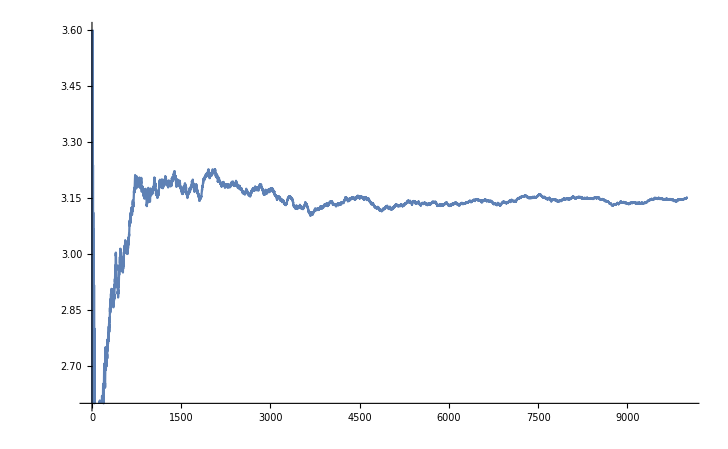

```mathematica
BuffonData[10000,2,100,3]
```

```mathematica
(***********************************************************************************************************)
```

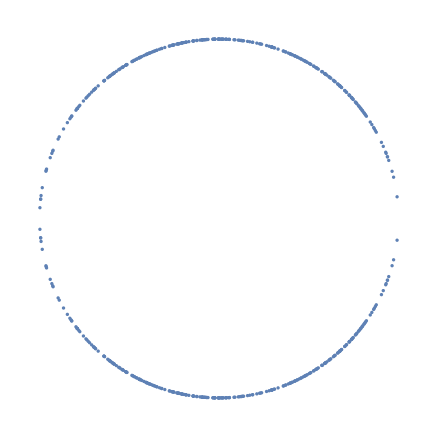

```mathematica
ListPlot[Flatten[Table[{x,#}&/@SolveValues[x^2+y^2==1,y]/.x->RandomReal[{-1,1}],300],1],Axes->False,AspectRatio->Automatic]
```

```mathematica
(***********************************************************************************************************)
```

```mathematica
Assuming[{L>0,w>0,0<θ<Pi/2},Integrate[Integrate[Piecewise[{{4/(w π), 0 <= x <= w/2}}], {x, 0, (L*Sin[θ])/2}] ,{θ,0,Pi/2}]//FullSimplify]
```

Piecewise[{{(2 L)/(π w), L≤w}, {(2 (L-√((L-w) (L+w))+w ArcCos[w/L]))/(π w), True}}]

```mathematica
(***********************************************************************************************************)
```

```mathematica
FullSimplify[ReplaceAll[Piecewise[{{(2 l)/(π w), l≤w}, {(2 (l-√((l-w) (l+w))+w ArcCos[w/l]))/(π w), l>w}}],{w->l/z}],z>1]
```

Piecewise[{{(2 z)/π, z≤1}, {(2 (z-√(-1+z^2)+ArcSec[z]))/π, z>1}}]

```mathematica
(***********************************************************************************************************)
```

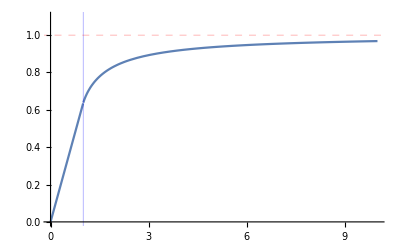

```mathematica
Plot[Piecewise[{{(2 z)/π, z<=1}, {(2 (z-√(-1+z^2)+ArcSec[z]))/π, z>1}}],{z,0,10},GridLines->{{{1,Directive[Blue,Thick]}},{{1,Directive[Dashed,Red,Thick]}}},PlotRange->{0,1.1},Ticks->{Range[0,14],Automatic}]
```

```mathematica
(***********************************************************************************************************)
```

```mathematica
Buffon[NumberOfNeedles,NeedleSize,SurfaceDimension,GridWidth,Options_Show_True_Parallelize]
```

```mathematica
Buffon[30,2,25,3,Show->True]
```

```mathematica
Buffon[10000,2,25,3,Show->Parallelize]
```